```mathematica
Pulsar Hotspots             
2019.05
```

### The Quadrudipole ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___ ___

```mathematica
rotateθ[inc_]:=ArcCos[Cos[θ]Cos[inc]-Sin[θ]Cos[ϕ]Sin[inc]];
rotateϕ[inc_]:= ArcTan[(Sin[θ]Cos[ϕ]Cos[inc]+Cos[θ]Sin[inc]),(Sin[θ]Sin[ϕ])];   
θprime = rotateθ[iota];
ϕprime=rotateϕ[iota];

MOI=II*M*Rstar^2;
OmegaZ =(2*MOI)/Rstar^3 Omega;

f = 1-(2M)/r; 
R1=-3/(2r)((3-4f+f^2+4Log[√f])/(1-f)^3);
R2 = -10/(3 r^2)((17-9f-9 f^2+f^3+12(1+3f)Log[√f])/(1-f)^5);

Δ1 =Rstar*(R1/.{r->Rstar});
Δ2 = Rstar^2*(R2/.{r->Rstar});
mu2= mu*q(Rstar Δ1/Δ2);

(*NB: αquad = (B1*Rstar^3)/Δ1 R1 (Sin[θprime])^2 +  (B2*Rstar^4)/Δ2 R2 Cos[θprime](Sin[θprime])^2
and mu = B1*Rstar^3/Δ1 *)

αdip=mu*R1*(Sin[θprime])^2; 

αquad = mu*R1*(Sin[θprime])^2 +  mu2*R2*Cos[θprime](Sin[θprime])^2;

α0=√(3/2)mu*Omega(1+1/5(Sin[iota])^2);

β= ϕprime;  

α=αquad;

pm= If[θprime<Pi/2,1,-1];
Lambda=Piecewise[{{0,α≤0},{-2Omega(BesselJ[0,2ArcSin[√(α/α0)]]Cos[iota] -pm*BesselJ[1,2ArcSin[√(α/α0)]]Cos[β]*Sin[iota]),0<α<α0 }}];

(*Jt[α_,β_]:=(√f) (Omega-OmegaZ)/(r^2 f)*( ∂_θ α ∂_θ (∂_ϕ β) - ∂_θ β ∂_θ (∂_ϕ α )- ∂_ϕ α((∂_θ (Sin[θ]∂_θ β))/Sin[θ]) + ∂_ϕ β(f∂_r (r^2∂_r α)+(∂_θ (Sin[θ]∂_θ α))/Sin[θ])); 
Jr[α_,β_]:= Lambda[α,β]/(√(r^2 f)(r*Sin[θ]))(∂_θ α ∂_ϕ β - ∂_θ β ∂_ϕ α);
Jθ[α_,β_]:= Lambda[α,β]/(r*Sin[θ])(-∂_r α ∂_ϕ β);
Jϕ[α_,β_]:= Lambda[α,β]/r(∂_r α ∂_θ β);*)

Jt= (√f) (Omega-OmegaZ)/(r^2 f)( D[α, θ] D[D[β, ϕ], θ] - D[β, θ] D[D[α, ϕ], θ] - D[α, ϕ](D[(Sin[θ]D[β, θ]), θ]/Sin[θ]) + D[β, ϕ](f D[(r^2 D[α, r]), r]+D[(Sin[θ]D[α, θ]), θ]/Sin[θ])); 
Jr= Lambda/(√(r^2 f)(r*Sin[θ]))(D[α, θ] D[β, ϕ] - D[β, θ] D[α, ϕ]);
Jθ= Lambda/(r*Sin[θ])(-D[α, r] D[β, ϕ]);
Jϕ= Lambda/r(D[α, r] D[β, θ]);

surfacecurrent = {Jt,Jr,Jθ,Jϕ} /.r->Rstar;

JmuJmu = Evaluate[(-Jt^2+Jr^2+Jθ^2+Jϕ^2)/.{r->Rstar}];
Jsquared = Evaluate[(Jr^2+Jθ^2+Jϕ^2)/.{r->Rstar}];
```

```mathematica
___ ___ ___ ___ ___ __________________________________________
```

```mathematica
(* convert to natural units *)
GMoverc2=1.47662; GMoverc3 = 4.92549*10^(-6);
radius = 11; mass = 1.5; spinf = 300;
R = radius/GMoverc2
compactness = mass/R
Omega=(2*Pi*GMoverc3)*spinf
epsilon = Omega*R
```

```mathematica
(* calculate the size of the polar caps *)

ϵ=0.0474; Co=0.1;
f=1-Co;
iota=(Pi/2);
sols =Solve[-3/2((3-4f+f^2+4Log[√f])/(1-f)^3)*(Sin[angle])^2 == √(3/2)ϵ(1+1/5(Sin[iota])^2) ,angle];
θmax =(angle /.sols[[2]]) * (180.0/Pi)
```

```mathematica
(* ----------------------- *)
```

```mathematica
PlotCap2[inclination_]:=
Module[{x,y,θprime,ϕprime,f,JJ,αmess},
Rstar=1;M=0.2;Omega=0.07;
(*note that for the dipole plots we can let iota=inclination, since we'r always looking down the barrel at the north pole*)
θθ=rotateθ[-inclination]/.{θ->θprime,ϕ->ϕprime}; (* inverse transformation is just minus the original *)
ϕϕ=rotateϕ[-inclination]/.{θ->θprime,ϕ->ϕprime};
rotmap = {θ->θθ,ϕ->ϕϕ};
patchmap ={θprime->ArcSin[√(x^2+y^2)/Rstar],ϕprime-> ArcTan[x,y]};
(*for the ring, patchmap is piece-wise to avoid problem if patchsize > √2/2 *)(*patchmap =If[(√(x^2+y^2)/Rstar)<1,{θprime->ArcSin[√(x^2+y^2)/Rstar],ϕprime-> ArcTan[x,y]},{θprime->x,ϕprime->y }];*) (*transform to cartesian coordinates to plot the patch*)
patchsize = 0.32*Rstar;
f = 1-(2M)/r; 
αmess=-3/2((3+2Log[f]-4f+f^2)/(1-f)^3)/.r->Rstar; 
sinθmax = ((√(3/2)(1+(Sin[inclination]^2/5))*Omega*Rstar)/αmess )^(1/2);(* the angle at which α=α0 *)
(*sinθmax=0.249597;*)   (*must specify sinθmax for quadrudipole, and also sinθmin for a ring*)
sinθmin=0;
J0=0.2728168; (*max value of the aligned dipole*)
k=1;cf=ColorData["SunsetColors"][(0.8*#)^2(*(Exp[k*#]-1)/(Exp[k]-1)*)]&;  (*non-linear color scaling to show color variation better*)
Show[
DensityPlot[((newJ/J0)^(1/8)/.rotmap)/.patchmap,{x,-patchsize,patchsize},{y,-patchsize,patchsize},RegionFunction->Function[{x,y},sinθmin≤(√(x^2+y^2)/Rstar)<sinθmax],ColorFunction->cf,ColorFunctionScaling->False, PlotLegends->False(*BarLegend[{cf,{0,1.25}},LegendMarkerSize->200,LabelStyle->{GrayLevel[0.3],FontSize->16}]*),PlotPoints-> 250,FrameTicks->None,PlotRange->{{-patchsize,patchsize},{-patchsize,patchsize}}]
]
]
```

```mathematica
(*C=M/R=0.2 and ϵ=ΩR=0.07 represent our canonical values: M=1.5Msolar, R=11km, Omega=300Hz*)
inputparams = {Rstar->1,M->0.2,Omega->0.07,II->2/5,mu->1,q->1.5,iota->30*(Pi/180)};
myJsq=Jsquared /.inputparams;
myJmu = JmuJmu /.inputparams;
newJ=Piecewise[{{myJsq,myJmu>=0},{0,myJmu<0}}]; 
alpha = (mu*R1*Sinθp^2 +  mu2*R2*(-√(1-Sinθp^2))Sinθp^2)/.{r->Rstar}/.inputparams;
Sinθmax=Solve[alpha==α0/.inputparams,Sinθp]
Sinθmin=Solve[alpha==0/.inputparams,Sinθp]
Jmax=newJ /.{θ->-32.4*(Pi/180),ϕ->0};
Tmax = (Jmax/0.2728168)^(1/8);
```

{{Sinθp→-0.798813},{Sinθp→0.-0.328111 ⅈ},{Sinθp→0.+0.328111 ⅈ},{Sinθp→0.798813}}

{{Sinθp→-0.745356},{Sinθp→0.},{Sinθp→0.745356}}

-Graphics-

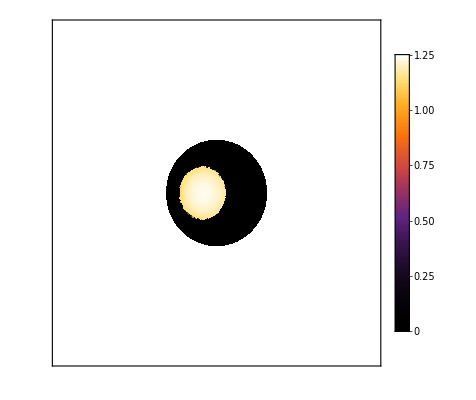

-Graphics-

```mathematica
inca=30*(Pi/180);
PlotCap2[inca]
```

```mathematica
(*q0.75s*)
```

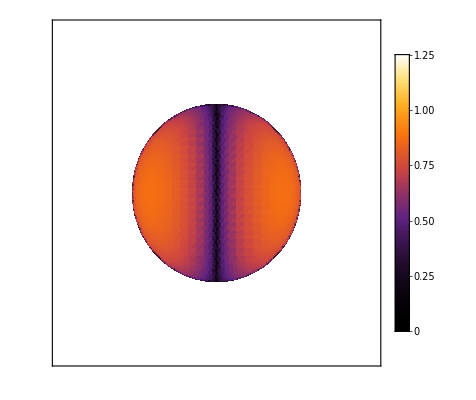

```mathematica
(*q0,i30*)
```

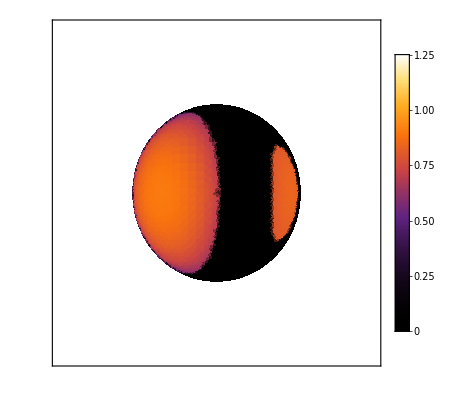

```mathematica
(*q0,i75*)
```

```mathematica
PlotStrip[inclination_]:=
Module[{x,y,θprime,ϕprime,f,JJ,αmess},
Rstar=1;(*M=1.5;Omega=0.00928;ϵ=Omega*Rstar;*)
θθ=rotateθ[-inclination]/.{θ->θprime,ϕ->ϕprime}; (* inverse transformation is just minus the original *)
ϕϕ=rotateϕ[-inclination]/.{θ->θprime,ϕ->ϕprime};
rotmap = {θ->θθ,ϕ->ϕϕ};
patchmap ={θprime->x,ϕprime->y};  (*transform to cartesian coordinates to plot the patch*)
k=1;cf=ColorData["SunsetColors"][(0.8*#)^2]&; 
J0=0.2728168;
DensityPlot[((newJ/J0)^(1/8)/.rotmap)/.patchmap,{x,2.215,2.3},{y,-Pi,Pi},(*RegionFunction->Function[{x,y},0.6<y<0.8],*)ColorFunction->cf,ColorFunctionScaling->False,PlotLegends->Automatic,PlotPoints-> 300,AspectRatio->2, FrameTicks->None,PlotRange->All]]
```

```mathematica
PlotStrip[30*(Pi/180)]
```

-Graphics-

```mathematica
RunSim2[i_]:= (
inputparams = {Rstar->1,M->0.2,Omega->0.07,II->2/5,mu->1,q->0,iota->i};
myJsq=Jsquared /.inputparams;
myJmu = JmuJmu /.inputparams;
newJ=Piecewise[{{myJsq,myJmu>=0},{0,myJmu<0}}];
PlotCap2[i]
);
```

```mathematica
(*FINAL EXPORT*)
Export["dipole_final.png",GraphicsGrid[
{{RunSim2[Pi/12],RunSim2[2Pi/12],RunSim2[3Pi/12]},
{RunSim2[4Pi/12],RunSim2[5Pi/12],RunSim2[6Pi/12]}
}],ImageResolution->1000
]
```

dipole_final.png

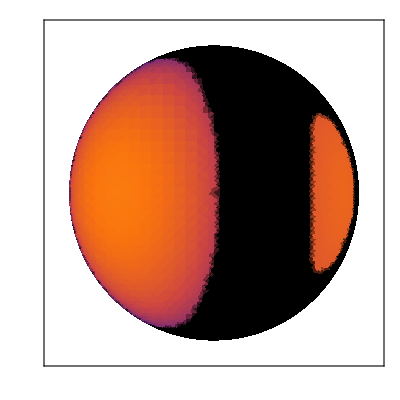

```mathematica
RunSim2[5Pi/12]
```